# γ decaying into q qb

## Load FeynCalc and the necessary add-ons or other packages

```mathematica
description="γ -> q qb, EW, total decay rate, 1-loop";
If[ $FrontEnd === Null,
	$FeynCalcStartupMessages = False;
	Print[description];
];
If[ $Notebooks === False,
	$FeynCalcStartupMessages = False
];
$LoadAddOns={"FeynArts"};
<<FeynCalc`
$FAVerbose = 0;

FCCheckVersion[9,3,1];

SetOptions[FourVector,FeynCalcInternal->False];
```

FeynCalc is already loaded! If you are trying to reload FeynCalc or load FeynArts, TARCER, PHI, FeynHelpers or any other add-on, please restart the kernel.

$Aborted

## EFT - Generate Feynman diagrams - tree level

Here we consider only the dominant contribution from the top quark mass. However, it is trivial to include also loops from other quark flavors.

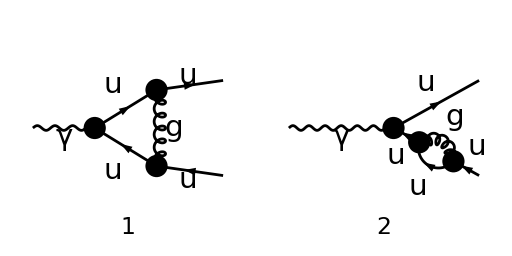

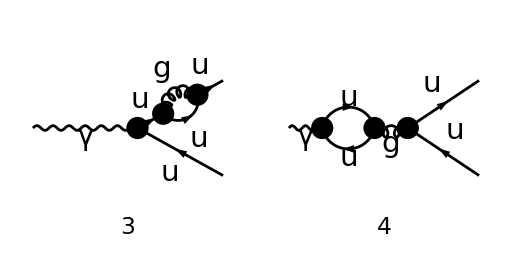

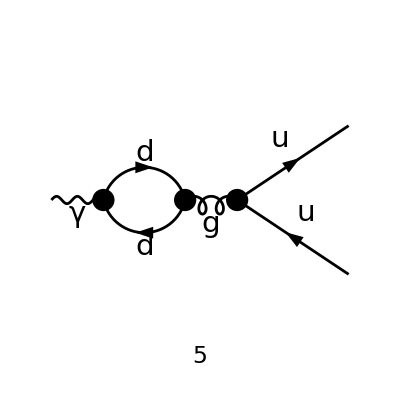

```mathematica
diags2 = InsertFields[CreateTopologies[1,1 -> 2,ExcludeTopologies->Tadpoles], 
	{V[1]} -> {F[3,{1}],-F[3,{1}]}, InsertionLevel ->{Particles},Model->"SMQCD",
	ExcludeParticles->{U[_],S[_],V[1],V[2],V[3],F[_,{2|3}]}];

Paint[diags2, ColumnsXRows -> {2, 1}, Numbering -> Simple,
	SheetHeader->None,ImageSize->{512,256}];
```

## Obtain the amplitudes

```mathematica
FCClearScalarProducts[];
```

```mathematica
(*Vertex correction*)
```

```mathematica
amp[a]=FCFAConvert[CreateFeynAmp[DiagramExtract[diags2,{1}],PreFactor->-1],IncomingMomenta->{pH},
	OutgoingMomenta->{kq,kqb},LoopMomenta->{k},List->False,Contract->True,
	DropSumOver->True,SMP->True,UndoChiralSplittings->True]/.Momentum[Polarization[pH,Complex[0,1]]]->LorentzIndex[μ]/.k->k+kq
```

-(2 e g_s^2 T_Col2Col4^Glu4 T_Col4Col3^Glu4 (φ(OverBar[kq],m_u)).(γ̄)^Lor3.(γ̄·(k̄+OverBar[kq])+m_u).(γ̄)^μ.(γ̄·(k̄-OverBar[kqb])+m_u).(γ̄)^Lor3.(φ(-OverBar[kqb],m_u)))/(3 ((k̄+OverBar[kq])^2-m_u^2).(k̄)^2.((k̄-OverBar[kqb])^2-m_u^2))

```mathematica
amp[b]=amp[a]//SUNSimplify;
```

```mathematica
amp[c]=amp[b]//DiracSimplify;
```

```mathematica
amp[c]/.FeynAmpDenominator[___]->1/Q//Simplify
```

1/(3 Q)4 e C_F g_s^2 δ_Col2Col3 (-(2 (k̄·OverBar[kq])-2 (k̄·OverBar[kqb])+(k̄)^2-2 (OverBar[kq]·OverBar[kqb])) (φ(OverBar[kq],m_u)).(γ̄)^μ.(φ(-OverBar[kqb],m_u))+2 ((k̄)^μ+OverBar[kq]^μ-OverBar[kqb]^μ) (φ(OverBar[kq],m_u)).(γ̄·k̄).(φ(-OverBar[kqb],m_u))+m_u ((φ(OverBar[kq],m_u)).(γ̄)^μ.(γ̄·k̄).(φ(-OverBar[kqb],m_u))+(φ(OverBar[kq],m_u)).(γ̄·k̄).(γ̄)^μ.(φ(-OverBar[kqb],m_u))-4 (k̄)^μ (φ(OverBar[kq],m_u)).(φ(-OverBar[kqb],m_u))))

```mathematica
(*Self energy no quark*)
```

```mathematica
amp[0]=FCFAConvert[CreateFeynAmp[DiagramExtract[diags2,{3}],PreFactor->-1],IncomingMomenta->{pH},
	OutgoingMomenta->{kq,kqb},LoopMomenta->{k},List->False,Contract->True,
	DropSumOver->True,SMP->True,UndoChiralSplittings->True]/.Momentum[Polarization[pH,Complex[0,1]]]->LorentzIndex[μ]
```

-(2 e g_s^2 T_Col2Col4^Glu4 T_Col4Col3^Glu4 (φ(OverBar[kq],m_u)).(γ̄)^Lor3.(m_u-γ̄·k̄).(γ̄)^Lor3.(γ̄·OverBar[kq]+m_u).(γ̄)^μ.(φ(-OverBar[kqb],m_u)))/(3 (OverBar[kq]^2-m_u^2) ((k̄)^2-m_u^2).(k̄+OverBar[kq])^2)

```mathematica
amp[1]=amp[0]//SUNSimplify;
```

```mathematica
amp[2]=amp[1]//DiracSimplify;
```

```mathematica
amp[2]/.FeynAmpDenominator[___]->1/Q1//Simplify
```

-(8 e C_F g_s^2 δ_Col2Col3 (k̄·OverBar[kq]+2 m_u^2) (φ(OverBar[kq],m_u)).(γ̄)^μ.(φ(-OverBar[kqb],m_u)))/(3 Q1^2)

```mathematica
(*Self energy no anti-quark*)
```

```mathematica
amp[00]=FCFAConvert[CreateFeynAmp[DiagramExtract[diags2,{2}],PreFactor->-1],IncomingMomenta->{pH},
	OutgoingMomenta->{kq,kqb},LoopMomenta->{k},List->False,Contract->True,
	DropSumOver->True,SMP->True,UndoChiralSplittings->True]/.Momentum[Polarization[pH,Complex[0,1]]]->LorentzIndex[μ]
```

-(2 e g_s^2 T_Col2Col4^Glu4 T_Col4Col3^Glu4 (φ(OverBar[kq],m_u)).(γ̄)^μ.(m_u-γ̄·OverBar[kqb]).(γ̄)^Lor3.(γ̄·k̄+m_u).(γ̄)^Lor3.(φ(-OverBar[kqb],m_u)))/(3 (OverBar[kqb]^2-m_u^2) ((k̄)^2-m_u^2).(k̄+OverBar[kqb])^2)

```mathematica
amp[11]=amp[00]//SUNSimplify;
```

```mathematica
amp[22]=amp[11]//DiracSimplify;
```

```mathematica
amp[22]/.FeynAmpDenominator[___]->1/Q2//Simplify
```

-(8 e C_F g_s^2 δ_Col2Col3 (k̄·OverBar[kqb]+2 m_u^2) (φ(OverBar[kq],m_u)).(γ̄)^μ.(φ(-OverBar[kqb],m_u)))/(3 Q2^2)